# Coherent applying of a matrix on a vector

calculate matrix applying on a vector, A.x, using quantum circuits

## Example Content

In the realm of quantum linear solvers, a typical procedure involves designing a circuit that yields the equivalent outcome of applying a n×n matrix, like A, to a n-element vector, such as x. Essentially, this entails executing the operation A.x through quantum implementation.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

Given n-qubits, the dimension of A will be 2^n×2^n. Create a random operator for 3-qubit case:

```mathematica
n=3;
a=RandomReal[{-1,1},{2^n,2^n}];
A=QuantumOperator[a];
```

Find the Pauli decomposition of A:

```mathematica
pauliDecompose=A["PauliDecompose"]
```

<|XXX→0.211297+0. ⅈ,XXY→0.-0.110715 ⅈ,XXZ→0.198033+0. ⅈ,XXI→-0.0803537+0. ⅈ,XYX→0.-0.0877234 ⅈ,XYY→-0.107238+0. ⅈ,XYZ→0.+0.0203499 ⅈ,XYI→0.+0.0981309 ⅈ,XZX→0.0598082+0. ⅈ,XZY→0.-0.142928 ⅈ,XZZ→-0.171679+0. ⅈ,XZI→-0.151295+0. ⅈ,XIX→-0.258682+0. ⅈ,XIY→0.+0.0114687 ⅈ,XIZ→-0.22355+0. ⅈ,XII→0.0388+0. ⅈ,YXX→0.+0.320737 ⅈ,YXY→-0.0448872+0. ⅈ,YXZ→0.+0.412652 ⅈ,YXI→0.-0.0655296 ⅈ,YYX→-0.200803+0. ⅈ,YYY→0.+0.384275 ⅈ,YYZ→-0.0289906+0. ⅈ,YYI→0.0256568+0. ⅈ,YZX→0.+0.341995 ⅈ,YZY→-0.114837+0. ⅈ,YZZ→0.-0.0336461 ⅈ,YZI→0.-0.0385934 ⅈ,YIX→0.+0.138818 ⅈ,YIY→0.199916+0. ⅈ,YIZ→0.+0.499497 ⅈ,YII→0.-0.0537861 ⅈ,ZXX→-0.325381+0. ⅈ,ZXY→0.+0.0876408 ⅈ,ZXZ→0.140522+0. ⅈ,ZXI→0.0942942+0. ⅈ,ZYX→0.-0.209835 ⅈ,ZYY→0.0881496+0. ⅈ,ZYZ→0.-0.105072 ⅈ,ZYI→0.-0.153355 ⅈ,ZZX→0.108864+0. ⅈ,ZZY→0.-0.0381291 ⅈ,ZZZ→-0.119564+0. ⅈ,ZZI→-0.0789658+0. ⅈ,ZIX→-0.198655+0. ⅈ,ZIY→0.+0.201184 ⅈ,ZIZ→0.0572329+0. ⅈ,ZII→-0.0628151+0. ⅈ,IXX→-0.20364+0. ⅈ,IXY→0.-0.119644 ⅈ,IXZ→-0.0148875+0. ⅈ,IXI→-0.263927+0. ⅈ,IYX→0.+0.0190936 ⅈ,IYY→0.14018+0. ⅈ,IYZ→0.-0.656842 ⅈ,IYI→0.+0.0806824 ⅈ,IZX→0.188248+0. ⅈ,IZY→0.+0.0737358 ⅈ,IZZ→0.161554+0. ⅈ,IZI→-0.42743+0. ⅈ,IIX→0.211465+0. ⅈ,IIY→0.+0.12888 ⅈ,IIZ→0.0794086+0. ⅈ,III→-0.136596+0. ⅈ|>

Find the binary length of terms in Pauli decomposition

```mathematica
L=Log2@Length[pauliDecompose]
```

6

Create a Multiplexer, using the keys of the Pauli decomposition:

```mathematica
mp=QuantumCircuitOperator["Multiplexer"[Sequence@@Keys[pauliDecompose]]];
```

Show the circuit diagram:

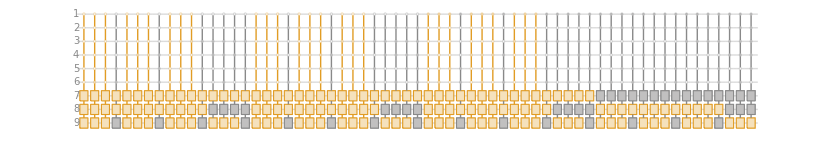

```mathematica
mp["Diagram","ShowGateLabels"->False]
```

Create a quantum state using the square-root of values in the Pauli decomposition:

```mathematica
ancillary=QuantumState[Sqrt@Values[pauliDecompose]]
```

QuantumState[…]

Create a random n-element vector:

```mathematica
x=RandomReal[{-1,1},2^n]
```

{-0.612068,-0.368019,0.465311,0.960787,-0.320024,-0.0583026,-0.397421,-0.189865}

Create a circuit for implementing A.x:

```mathematica
qc=N@QuantumCircuitOperator[{ancillary,QuantumState[x]->Range[L+1,L+1+n],mp,SuperDagger[(ancillary["Conjugate"])]}];
```

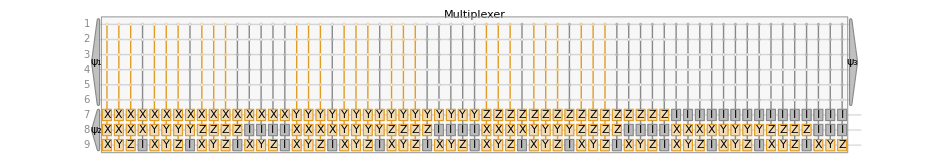

```mathematica
qc["Diagram"]
```

Calculate the AmplitudesList of the circuit:

```mathematica
qc[]["AmplitudesList"]
```

{-1.52781+0. ⅈ,0.127506+0. ⅈ,-0.512799+0. ⅈ,0.804974+0. ⅈ,1.01403+0. ⅈ,-0.398952+0. ⅈ,0.590336+0. ⅈ,-0.306825+0. ⅈ}

Calculate A.x directly:

```mathematica
a.x
```

{-1.52781,0.127506,-0.512799,0.804974,1.01403,-0.398952,0.590336,-0.306825}

Check the results are the same

```mathematica
%-%%//Chop
```

{0,0,0,0,0,0,0,0}

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

```mathematica
ResourceData[{{}},"NameOfContent"]=xxxx
```

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

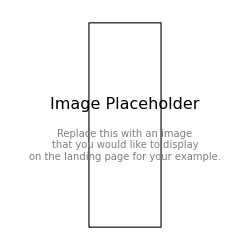

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

keyword 1

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 System Modeling
 Video Processing
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Signal Processing
 Text & Language Processing
 Visualization & Graphics
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Social Sciences
 Time-Related Computation
 Quantum Computation

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.